```mathematica
1000*331*10^-6//N
```

0.331

```mathematica
data=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/bessel_results.txt","table"];
Dimensions[data]
```

{200,3}

```mathematica
FuncionPrueba[n_,x_]:=(SphericalBesselJ[n,x]*x+SphericalBesselY[n,x]*x)/(SphericalBesselJ[n,x]*x-SphericalBesselY[n,x]*x)*BesselK[n,x];
```

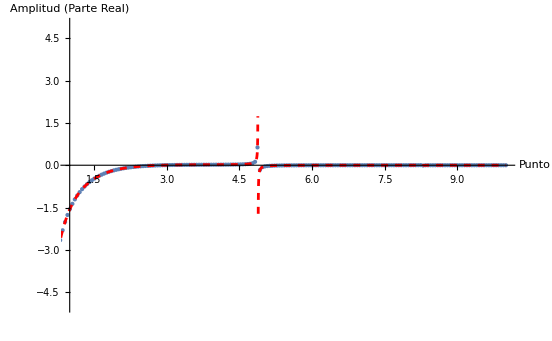

```mathematica
(*Graficar la parte real de los resultados*)realPlot=ListPlot[Transpose[{data[[All,1]],data[[All,2]]}],PlotRange->{{1,10},{-5,5}},PlotStyle->PointSize[Medium],AxesLabel->{"Punto","Amplitud (Parte Real)"},Joined->False];
Show[realPlot,Plot[Re[FuncionPrueba[2,x]],{x,0,10},PlotStyle->{Red,Dashed},PlotPoints->40,PlotRange->{-5,5}]]
```